```mathematica
15m the water pressure was 51 psi
```

765 m pressure psi the was water

```mathematica
25m the water pressure was 61.5 psi
```

1537.5 m pressure psi the was water

```mathematica
35m the water pressure was 69 psi
```

2415 m pressure psi the was water

```mathematica
f[a_, b_]:=(51-(15a+b))^2+(61.5-(25a+b))^2+(69-(35a+b))^2
```

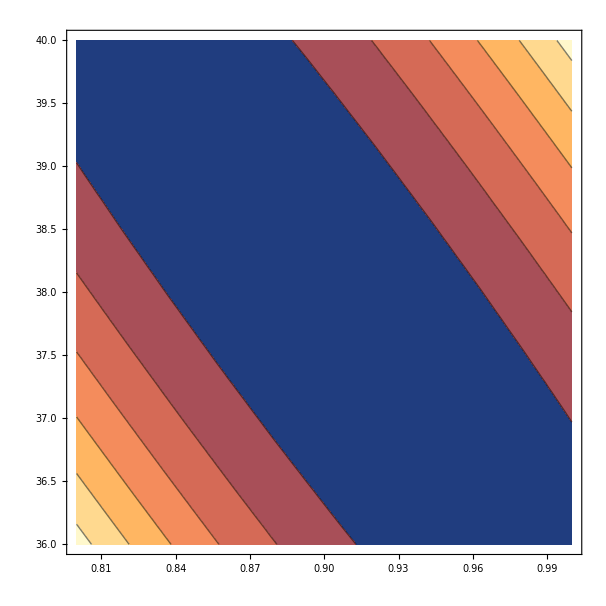

```mathematica
ContourPlot[f[a, b], {a, 0.8, 1.0 }, {b, 36,40}]
```

```mathematica
Minimize[f[a, b],{a, b}]
```

Minimize::ivar: 16 is not a valid variable.

Minimize[(-491-b)^2+(-338.5-b)^2+(-189-b)^2,{16,b}]

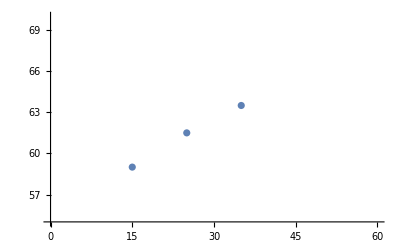

```mathematica
plot1=ListPlot[{{15, 59}, {25, 61.5}, {35, 63.5}}, PlotRange->{{0, 60},{55, 70}}]
```

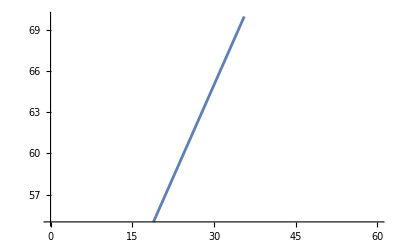

```mathematica
plot2=Plot[0.9*t + 38, {t, 0, 60}, PlotRange->{{0, 60},{55, 70}}]
```

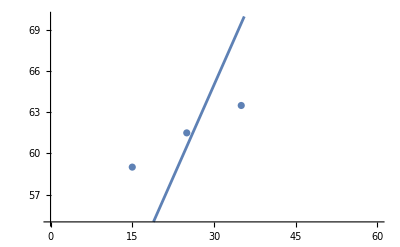

```mathematica
Show[plot1, plot2]
```